```mathematica
Quit[]
```

```mathematica
<<pkg`
```

```mathematica
(*User supplied data*)
m1=5/2;m2=1; λf=2; ϵ=3/1000//N;
Ri=2{ 1,1,1};
PPi=1{1/2,-1/2,1/3};
S1i={0,1,1}√ϵ;
S2i={1,-3/10,0}√ϵ;
(*end of user supplied  data*)


(*(*User supplied data*)
m1=1.5;m2=1; ϵ=N[3/1000];  λf=2;
Ri={-1,.5,1.5};
PPi=.1{1,-4,1};
S1i=√ϵ{1,1,1.3};
S2i=√ϵ{-7.5,-1.5,4.2}; 
(*end of user supplied  data*)
*)
```

# frequency

```mathematica
fr= frequency[m1,m2,Ri,PPi,S1i,S2i,ϵ];
Energy=fr[[1]]
frq=fr[[2]]
jcm=fr[[3]]
sfarray=fr[[4]]
```

-0.297117

{0.000307675,0.,0.217251,0.215805,0.000390352}

{{1.,0.,0.,0.,0.},{0.,1.,0.,0.,0.},{0.,0.,1.,0.,0.},{0.,0.,-1.0081,4.63382,-0.000423264},{-0.788199,0.,0.776242,0.,0.234}}

{0.,0.,-5.42101×10^-20,1.,0.}

# Compare flows under commuting constants with numerics

```mathematica
Jflow[m1,m2,Ri,PPi,S1i,S2i,λf,ϵ]-NmJflow[m1,m2,Ri,PPi,S1i,S2i,λf,ϵ]
Lflow[m1,m2,Ri,PPi,S1i,S2i,λf,ϵ]- NmLflow[m1,m2,Ri,PPi,S1i,S2i,λf,ϵ]
Jzflow[m1,m2,Ri,PPi,S1i,S2i,λf,ϵ]-NmJzflow[m1,m2,Ri,PPi,S1i,S2i,λf,ϵ]
Hflow[m1,m2,Ri,PPi,S1i,S2i,λf,ϵ]-NmHflow[m1,m2,Ri,PPi,S1i,S2i,λf,ϵ]
SeffLflow[m1,m2,Ri,PPi,S1i,S2i,λf,ϵ]-NmSeffLflow[m1,m2,Ri,PPi,S1i,S2i,λf,ϵ]
```

{{4.44166×10^-8,-1.39936×10^-7,1.25691×10^-8},{-1.98458×10^-8,-1.67792×10^-8,-2.07687×10^-8},{1.64819×10^-9,-2.26858×10^-9,1.02511×10^-9},{-9.43169×10^-10,-1.34088×10^-9,-1.09086×10^-9}}

{{4.43986×10^-8,-1.40043×10^-7,1.36583×10^-8},{-2.04945×10^-8,-1.70769×10^-8,-1.99249×10^-8},{0.,0.,0.},{0.,0.,0.}}

{{-1.43969×10^-7,3.8067×10^-8,0.},{9.51676×10^-9,3.59923×10^-8,0.},{-2.49263×10^-9,-1.45013×10^-9,0.},{-7.02336×10^-10,2.92767×10^-9,0.}}

{{-0.000353519,-0.000439894,-0.000176306},{-0.0000740366,-0.0000981669,-0.0000804519},{2.22934×10^-6,1.4833×10^-6,-1.48346×10^-6},{-0.0000685703,-0.0000469963,-0.0000613906}}

{{-5.23101×10^-8,1.33516×10^-7,-5.37614×10^-8},{-1.25003×10^-7,-7.04871×10^-9,1.77276×10^-7},{1.25575×10^-8,-1.21173×10^-9,1.24785×10^-8},{-3.38263×10^-7,6.54668×10^-7,-1.77812×10^-7}}

# check action J, Jz, L close loop

```mathematica
{Ri,PPi,S1i,S2i}-Jac1[m1,m2,Ri,PPi,S1i,S2i,2 π,ϵ] 
{Ri,PPi,S1i,S2i}-Jac2[m1,m2,Ri,PPi,S1i,S2i,2 π,ϵ]
{Ri,PPi,S1i,S2i}-Jac3[m1,m2,Ri,PPi,S1i,S2i,2 π,ϵ]
```

{{3.77476×10^-15,-5.77316×10^-15,2.88658×10^-15},{-5.55112×10^-16,-1.27676×10^-15,-7.21645×10^-16},{9.77533×10^-17,-6.93889×10^-17,8.32667×10^-17},{6.93889×10^-18,-8.32667×10^-17,-3.74704×10^-17}}

{{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.}}

{{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.}}

```mathematica
{Ri,PPi,S1i,S2i}-NmJac1[m1,m2,Ri,PPi,S1i,S2i,2 π,ϵ] 
{Ri,PPi,S1i,S2i}-NmJac2[m1,m2,Ri,PPi,S1i,S2i,2 π,ϵ]
{Ri,PPi,S1i,S2i}-NmJac3[m1,m2,Ri,PPi,S1i,S2i,2 π,ϵ]
```

{{1.0204×10^-7,-4.77733×10^-8,8.11728×10^-8},{4.31174×10^-10,-3.08595×10^-8,-5.51474×10^-9},{2.08946×10^-9,1.52151×10^-10,1.87815×10^-9},{3.35879×10^-10,-1.82434×10^-9,-5.13379×10^-11}}

{{2.28868×10^-11,1.30164×10^-7,0.},{3.25409×10^-8,-5.7217×10^-12,0.},{-1.78203×10^-9,1.78265×10^-9,0.},{2.31726×10^-9,1.24723×10^-9,0.}}

{{1.05942×10^-7,-5.5134×10^-8,7.90957×10^-8},{-1.10625×10^-9,-3.17055×10^-8,-6.20612×10^-9},{0.,0.,0.},{0.,0.,0.}}

# check action J4 close loop

```mathematica
{Ri,PPi,S1i,S2i}-Jac4[m1,m2,Ri,PPi,S1i,S2i,2 π ,ϵ]
{Ri,PPi,S1i,S2i}-NmJac4[m1,m2,Ri,PPi,S1i,S2i,2 π ,ϵ]
```

{{0.000968872,-0.00110089,0.000418605},{-0.0000799189,-0.000145097,-0.0000966181},{-0.0000153208,7.85262×10^-6,-7.84935×10^-6},{0.0000761924,0.0000724639,0.0000719654}}

{{-0.00145832,0.00335441,-0.000686116},{0.000306099,0.000778726,0.000394819},{-0.0000132922,9.49714×10^-6,-9.49388×10^-6},{7.56565×10^-6,0.0000251944,0.000010504}}

# Check action J5 close loop

```mathematica
{Ri,PPi,S1i,S2i}-Jac5[m1,m2,Ri,PPi,S1i,S2i,2 π ,ϵ]
{Ri,PPi,S1i,S2i}-NmJac5[m1,m2,Ri,PPi,S1i,S2i,2 π ,ϵ]
```

{{1.27831×10^-12,-1.0143×10^-12,-2.63345×10^-13},{-8.47877×10^-13,-3.80085×10^-13,7.01716×10^-13},{-4.2224×10^-12,3.1353×10^-12,-3.13635×10^-12},{2.52889×10^-12,5.22152×10^-13,2.33147×10^-12}}

{{-1.01323×10^-7,1.94294×10^-7,3.77743×10^-7},{1.35428×10^-7,-1.48643×10^-8,-6.10881×10^-8},{5.0482×10^-8,-4.81923×10^-9,2.85439×10^-8},{7.26946×10^-8,-5.44984×10^-7,-5.80735×10^-9}}

# action angle flow

```mathematica
tf=3000;
```

```mathematica
NmHflow[m1,m2,Ri,PPi,S1i,S2i,tf  ,ϵ]
Acflow[m1,m2,Ri,PPi,S1i,S2i,tf  ,ϵ]
Hflow[m1,m2,Ri,PPi,S1i,S2i,tf  ,ϵ]
```

{{3.13251,0.370801,2.74024},{-0.0435137,-0.636059,-0.162332},{0.025146,0.0222291,0.0698108},{0.013558,-0.0398193,-0.0387376}}

{{3.00875,0.78997,2.71756},{0.297363,-0.578761,0.139237},{0.0251405,0.0222475,0.0698069},{0.0134892,-0.0397452,-0.0387788}}

{{3.00875,0.789971,2.71756},{0.297363,-0.578761,0.139237},{0.0251405,0.0222475,0.0698069},{0.0134892,-0.0397452,-0.0387788}}

```mathematica
Clear[tf]
```

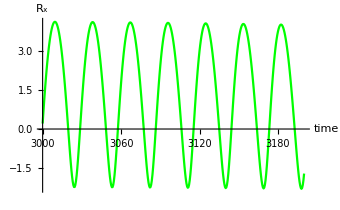

```mathematica
(*data=Table[{tf,Acflow[m1,m2,Ri,PPi,S1i,S2i,tf  ,ϵ][[1]][[1]]},{tf,3000,3200,0.5}];
Export["RXout.dat", data];*)
dataRX=Import["RXout.dat"];
aarx=ListPlot[dataRX,Joined->True,PlotRange->{{3000,3200},Automatic},PlotStyle->Green,AxesLabel->{"time","R_x"}]
```

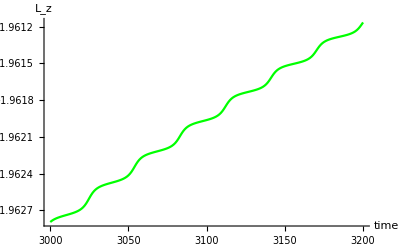

```mathematica
(*data=Table[{tf,(*Lz=*)Cross[Acflow[m1,m2,Ri,PPi,S1i,S2i,tf ,ϵ][[1]],Acflow[m1,m2,Ri,PPi,S1i,S2i,tf,ϵ][[2]]][[3]]},{tf,3000,3200,1}];
Export["LZout.dat", data];*)
dataLZ=Import["LZout.dat"];
aalz=ListPlot[dataLZ,Joined->True,PlotRange->{{3000,3200},Automatic},PlotStyle->Green,AxesLabel->{"time","L_z"}]
```

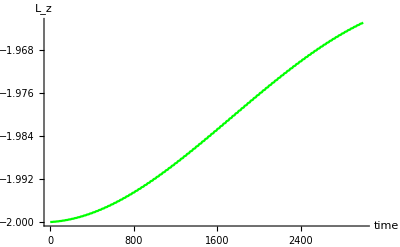

```mathematica
(*data=Table[{tf,(*Lz=*)Cross[Acflow[m1,m2,Ri,PPi,S1i,S2i,tf ,ϵ][[1]],Acflow[m1,m2,Ri,PPi,S1i,S2i,tf,ϵ][[2]]][[3]]},{tf,0,3000,3}];
Export["dtlzout.dat", data];*)
dtlz=Import["dtlzout.dat"];
aalz=ListPlot[dtlz,Joined->True,PlotRange->{{0,3000},Automatic},PlotStyle->Green,AxesLabel->{"time","L_z"}]
```

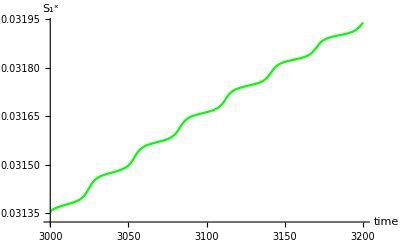

```mathematica
(*data=Table[{tf,(*S1x=*)Acflow[m1,m2,Ri,PPi,S1i,S2i,tf ,ϵ][[3]][[1]]},{tf,3000,3200,1}];
Export["S1Xout.dat", data];*)
dataS1X=Import["S1Xout.dat"];
aas1x=ListPlot[dataS1X,Joined->True,PlotRange->{{3000,3200},Automatic},PlotStyle->Green,AxesLabel->{"time","S_1^x"}]
```

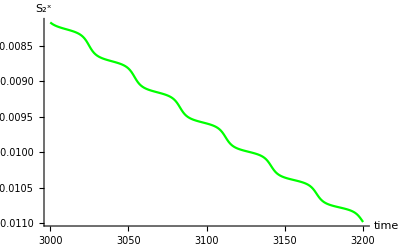

```mathematica
(*data=Table[{tf,(*S2x=*)Acflow[m1,m2,Ri,PPi,S1i,S2i,tf ,ϵ][[4]][[1]]},{tf,3000,3200,1}];
Export["S2Xout.dat", data];*)
dataS2X=Import["S2Xout.dat"];
aas2x=ListPlot[dataS2X,Joined->True,PlotRange->{{3000,3200},Automatic},PlotStyle->Green,AxesLabel->{"time","S_2^x"}]
```

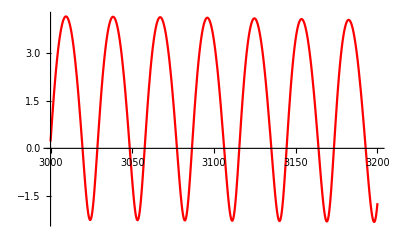
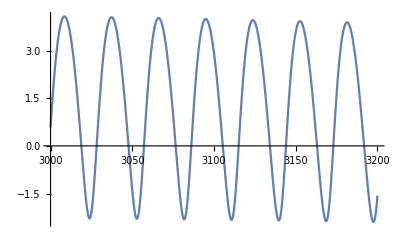
```mathematica
rxan=-Graphics-;(*Hflow[m1,m2,Ri,PPi,S1i,S2i,3500,ϵ][[1]]*)
rxnm=-Graphics-;(*NmHflow[m1,m2,Ri,PPi,S1i,S2i,3500,ϵ][[1]]*)
Show[{aarx,rxan,rxnm}]
```

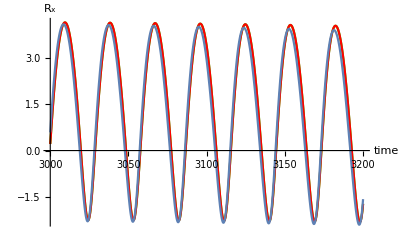

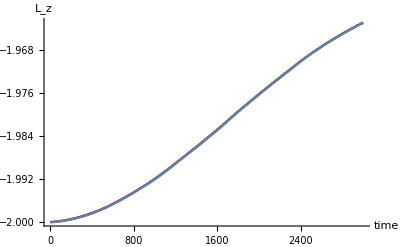

```mathematica
lzan=-Graphics-;(*Hflow[m1,m2,Ri,PPi,S1i,S2i,3500,ϵ][[2]]*)
lznm=-Graphics-;(*NmHflow[m1,m2,Ri,PPi,S1i,S2i,3500,ϵ][[2]]*)
Show[{aalz,lzan,lznm}]
```

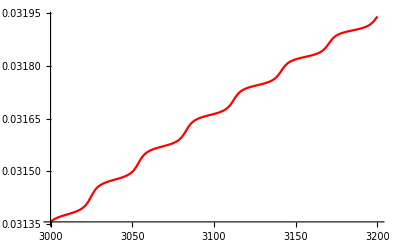
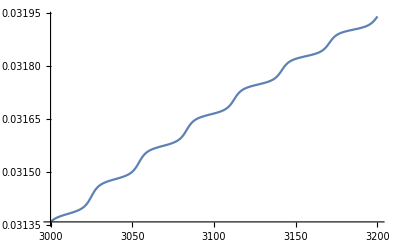
```mathematica
s1xan=-Graphics-;(*Hflow[m1,m2,Ri,PPi,S1i,S2i,3500,ϵ][[3]]*)
s1xnm=-Graphics-;(*NmHflow[m1,m2,Ri,PPi,S1i,S2i,3500,ϵ][[3]]*)
Show[{aas1x,s1xan,s1xnm}]
```

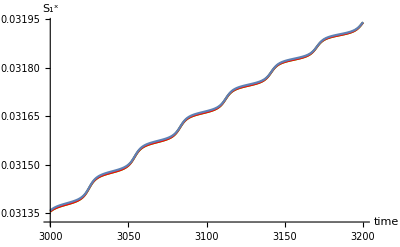

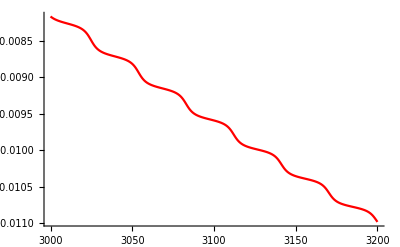
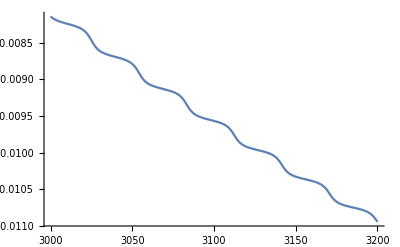
```mathematica
s2xan=-Graphics-;(*Hflow[m1,m2,Ri,PPi,S1i,S2i,3500,ϵ][[4]]*)
s2xnm=-Graphics-;(*NmHflow[m1,m2,Ri,PPi,S1i,S2i,3500,ϵ][[4]]*)
Show[{aas2x,s2xan,s2xnm}]
```